```mathematica
(1-a)p+a q/.{p->{t,1/t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a)/t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a Cos[t],(1-a)/t+a Sin[t]}
,{t,0,2π}]
,{a,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

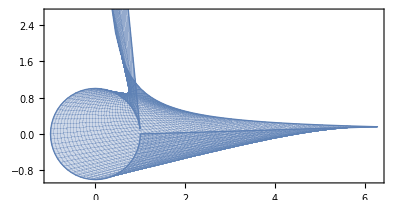

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a)/t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
FullSimplify[Norm[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}],{a,t}∈Reals]
```

√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2)

```mathematica
Integrate[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

$Aborted

```mathematica
NIntegrate[√((t-a t+a Cos[t])^2+(t-a t+a Sin[t])^2),{t,0,2π},{a,0,1}]
```

14.7543

```mathematica
14.754258100237308/π
```

4.69643

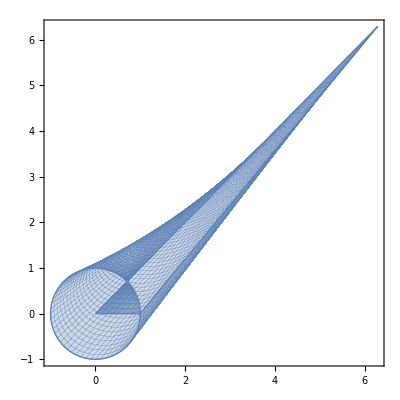

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
Norm[{Cos[t],Sin[t]}-{t,t}]
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
FullSimplify[Norm[{Cos[t],Sin[t]}-{t,t}],t∈Reals]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
FullSimplify[Norm[{Cos[t],Sin[t]}-{t,t}],t∈]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-2π,2π}]
```

57.6005

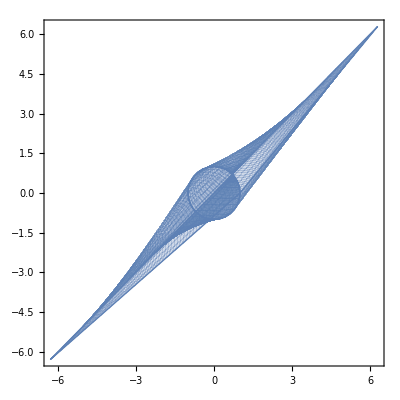

```mathematica
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,-2π,2π},{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{-t,-t},q->{Cos[t],Sin[t]}}
```

{-(1-a) t+a Cos[t],-(1-a) t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[
{-(1-a) t+a Cos[t],-(1-a) t+a Sin[t]}
,{t,0,2π}]
,{a,0,1}]
```

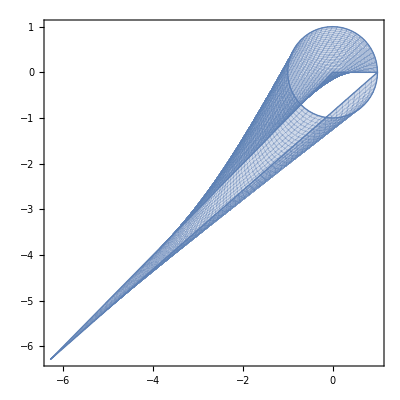

```mathematica
ParametricPlot[
{-(1-a) t+a Cos[t],-(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
```

```mathematica
FullSimplify[Norm[{-(1-a) t+a Cos[t],-(1-a) t+a Sin[t]}],{t,a}∈]
```

√(((-1+a) t+a Cos[t])^2+((-1+a) t+a Sin[t])^2)

```mathematica
NIntegrate[√(((-1+a) t+a Cos[t])^2+((-1+a) t+a Sin[t])^2),{a,0,1},{t,0,2π}]
```

15.2867

```mathematica
{ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}],
ParametricPlot[
{-(1-a) t+a Cos[t],-(1-a) t+a Sin[t]}
,{t,0,2π},{a,0,1}]
}
```

{-Graphics-,-Graphics-}